# Heavy Quarkonium Pseudoscalar Hybrid Correlator

Updated: 2017-8-16

## Preliminaries

```mathematica
project=scalarProject;
```

## No Interactions

### Preliminaries

```mathematica
1/4 Subscript[g, s] λ[a][α1,α2]dirac[γ[ρ]][i,j]leviCivita[μ,ρ,ω1,η1]CircleTimes[op[OverBar@Q,α1,i,x],op[Q,α2,j,x],op[G,a,ω1,η1,x]]
1/4 Subscript[g, s] λ[b][β1,β2]dirac[γ[σ]][k,l]leviCivita[ν,σ,ω2,η2]CircleTimes[op[OverBar@Q,β1,k,0],op[Q,β2,l,0],op[G,b,ω2,η2,0]]
I project Exp[I q x]CircleTimes[%%,%]
prefactorNone=%/.a_. b__CircleTimes:>a
opProductNone=%%/.a_. b__CircleTimes:>b
```

-1/4 op[Q̄,α1,i,x]⊗op[Q,α2,j,x]⊗op[G,a,ω1,η1,x] leviCivita[η1,μ,ρ,ω1] g_s dirac[γ[ρ]][i,j] λ[a][α1,α2]

-1/4 op[Q̄,β1,k,0]⊗op[Q,β2,l,0]⊗op[G,b,ω2,η2,0] leviCivita[η2,ν,σ,ω2] g_s dirac[γ[σ]][k,l] λ[b][β1,β2]

1/(16 q.q)ⅈ ⅇ^(ⅈ q x) op[Q̄,α1,i,x]⊗op[Q,α2,j,x]⊗op[G,a,ω1,η1,x]⊗op[Q̄,β1,k,0]⊗op[Q,β2,l,0]⊗op[G,b,ω2,η2,0] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^2 dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[b][β1,β2]

(ⅈ ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^2 dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[b][β1,β2])/(16 q.q)

op[Q̄,α1,i,x]⊗op[Q,α2,j,x]⊗op[G,a,ω1,η1,x]⊗op[Q̄,β1,k,0]⊗op[Q,β2,l,0]⊗op[G,b,ω2,η2,0]

```mathematica
DeleteCases[opProductNone/.CircleTimes->List,op[G,__]]
timeOrder[%,"fermion"];
%/.sortQuarkContractions/.zeroQuarkContractions;
wickFermionNone=%
```

{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q,β2,l,0]}

-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{}]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{}]-contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{op[Q,α2,j,x],op[Q̄,β1,k,0]}]-contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x]}]+contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,β2,l,0]}]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] normalOrder[{op[Q̄,β1,k,0],op[Q,β2,l,0]}]+normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q,β2,l,0]}]

```mathematica
DeleteCases[opProductNone,op[Q|OverBar@Q,__]]
%/.{op[G,a,μ_,ν_,x_]->op[F,a,μ,ν,x]+Subscript[g, s] structure[a,c,d]CircleTimes[op[A,c,μ,x],op[A,d,ν,x]],op[G,b,μ_,ν_,x_]->op[F,b,μ,ν,x]+Subscript[g, s] structure[b,e,f]CircleTimes[op[A,e,μ,x],op[A,f,ν,x]]};
Expand//@%;
%/.{CircleTimes[x__]:>timeOrder[List[x],"boson"]}//Expand;
%/.normalOrder[{_}]->0;
%//.{
normalOrder[{y___,op[F,a,μ_,ν_,x_],z___}]->normalOrder[{y,op[G,a,μ,ν,x],z}]-Subscript[g, s] structure[a,c,d]normalOrder[{y,op[A,c,μ,x],op[A,d,ν,x],z}],
normalOrder[{y___,op[F,b,μ_,ν_,x_],z___}]->normalOrder[{y,op[G,b,μ,ν,x],z}]-Subscript[g, s] structure[b,e,f]normalOrder[{y,op[A,e,μ,x],op[A,f,ν,x],z}]
};
wickBosonNone=Expand@%
```

op[G,a,ω1,η1,x]⊗op[G,b,ω2,η2,0]

contract[op[F,a,ω1,η1,x],op[F,b,ω2,η2,0]] normalOrder[{}]+normalOrder[{op[G,a,ω1,η1,x],op[G,b,ω2,η2,0]}]+contract[op[A,c,ω1,x],op[A,f,η2,0]] contract[op[A,d,η1,x],op[A,e,ω2,0]] normalOrder[{}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,e,ω2,0]] contract[op[A,d,η1,x],op[A,f,η2,0]] normalOrder[{}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,d,η1,x]] contract[op[A,e,ω2,0],op[A,f,η2,0]] normalOrder[{}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,e,ω2,0],op[A,f,η2,0]] normalOrder[{op[A,c,ω1,x],op[A,d,η1,x]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,d,η1,x],op[A,f,η2,0]] normalOrder[{op[A,c,ω1,x],op[A,e,ω2,0]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,d,η1,x],op[A,e,ω2,0]] normalOrder[{op[A,c,ω1,x],op[A,f,η2,0]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,f,η2,0]] normalOrder[{op[A,d,η1,x],op[A,e,ω2,0]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,e,ω2,0]] normalOrder[{op[A,d,η1,x],op[A,f,η2,0]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,d,η1,x]] normalOrder[{op[A,e,ω2,0],op[A,f,η2,0]}] structure[a,c,d] structure[b,e,f] g_s^2

### Perturbation Theory

```mathematica
prefactorNone
Cases[wickFermionNone,_. contract[op[Q,__,x],op[OverBar@Q,__,0]]normalOrder[{}],{1}]/.normalOrder[{}]->1//Total
Cases[wickBosonNone,_.contract[op[F,__,x],op[F,__,0]]normalOrder[{}],{1}]/.normalOrder[{}]->1//Total
pertNone=%%% %% %
```

(ⅈ ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^2 dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[b][β1,β2])/(16 q.q)

-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]

contract[op[F,a,ω1,η1,x],op[F,b,ω2,η2,0]]

-1/(16 q.q)ⅈ ⅇ^(ⅈ q x) contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] contract[op[F,a,ω1,η1,x],op[F,b,ω2,η2,0]] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^2 dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[b][β1,β2]

```mathematica
pertNone/.{
contract[op[Q,α_,i_,x],op[OverBar@Q,β_,j_,0]]:>Module[{p=p1},I Exp[-I p( x-0)]colourDelta[α,β]dirac[S[p,m]][i,j]],
contract[op[Q,α_,i_,0],op[OverBar@Q,β_,j_,x]]:>Module[{p=p2},I Exp[-I p( 0-x)]colourDelta[α,β]dirac[S[p,m]][i,j]],
contract[op[F,a_,μ_,ν_,x_],op[F,b_,ρ_,σ_,y_]]->Module[{p=p3},-I Exp[-I p3( x-y)]biColourDelta[a,b](metric[μ,ρ]p3[ν]p3[σ]-metric[μ,σ]p3[ν]p3[ρ]-metric[ν,ρ]p3[μ]p3[σ]+metric[ν,σ]p3[μ]p3[ρ])/(p3.p3)]
}//.diracIndexToMatrix;
Expand//@SToGamma//@%//.diracTraceLinear//.applyDiracTrace//.leviCivitaProductExpand;
pertIntegrandNone=Expand@%//.lorentzToDot//Simplify
```

(16 (-3+dim) ⅇ^(-ⅈ (p1-p2+p3-q) x) (2 p1.q (p2.q p3.p3-p2.p3 p3.q)+p1.p3 (-2 p2.q p3.q+2 p2.p3 q.q)+((-2+dim) m^2-(-4+dim) p1.p2) ((p3.q)^2-p3.p3 q.q)) g_s^2)/((m^2-p1.p1) (m^2-p2.p2) p3.p3 q.q)

```mathematica
pertIntegrandNone/.p3->-p1+p2+q;
%/.p2->p4-q/.{p1->k1,p4->k2};
top=Distribute[#,Plus,Dot]&//@Numerator[%]//.{Dot[-a_,b_]->-Dot[a,b],Dot[a_,-b_]->-Dot[a,b]}//.sortDot//Expand;
pertIntegrandFinalNone=top/Denominator[%%]
```

(96 m^2 (k1.q)^2 g_s^2-80 dim m^2 (k1.q)^2 g_s^2+16 dim^2 m^2 (k1.q)^2 g_s^2-96 k1.k2 (k1.q)^2 g_s^2+80 dim k1.k2 (k1.q)^2 g_s^2-16 dim^2 k1.k2 (k1.q)^2 g_s^2+96 (k1.q)^3 g_s^2-80 dim (k1.q)^3 g_s^2+16 dim^2 (k1.q)^3 g_s^2-96 (k1.q)^2 k2.k2 g_s^2+32 dim (k1.q)^2 k2.k2 g_s^2-192 m^2 k1.q k2.q g_s^2+160 dim m^2 k1.q k2.q g_s^2-32 dim^2 m^2 k1.q k2.q g_s^2+384 k1.k2 k1.q k2.q g_s^2-224 dim k1.k2 k1.q k2.q g_s^2+32 dim^2 k1.k2 k1.q k2.q g_s^2-192 (k1.q)^2 k2.q g_s^2+160 dim (k1.q)^2 k2.q g_s^2-32 dim^2 (k1.q)^2 k2.q g_s^2+96 m^2 (k2.q)^2 g_s^2-80 dim m^2 (k2.q)^2 g_s^2+16 dim^2 m^2 (k2.q)^2 g_s^2-96 k1.k1 (k2.q)^2 g_s^2+32 dim k1.k1 (k2.q)^2 g_s^2-96 k1.k2 (k2.q)^2 g_s^2+80 dim k1.k2 (k2.q)^2 g_s^2-16 dim^2 k1.k2 (k2.q)^2 g_s^2+96 k1.q (k2.q)^2 g_s^2-80 dim k1.q (k2.q)^2 g_s^2+16 dim^2 k1.q (k2.q)^2 g_s^2-96 m^2 k1.k1 q.q g_s^2+80 dim m^2 k1.k1 q.q g_s^2-16 dim^2 m^2 k1.k1 q.q g_s^2+192 m^2 k1.k2 q.q g_s^2-160 dim m^2 k1.k2 q.q g_s^2+32 dim^2 m^2 k1.k2 q.q g_s^2+96 k1.k1 k1.k2 q.q g_s^2-80 dim k1.k1 k1.k2 q.q g_s^2+16 dim^2 k1.k1 k1.k2 q.q g_s^2-288 (k1.k2)^2 q.q g_s^2+192 dim (k1.k2)^2 q.q g_s^2-32 dim^2 (k1.k2)^2 q.q g_s^2-96 k1.k1 k1.q q.q g_s^2+80 dim k1.k1 k1.q q.q g_s^2-16 dim^2 k1.k1 k1.q q.q g_s^2+192 k1.k2 k1.q q.q g_s^2-160 dim k1.k2 k1.q q.q g_s^2+32 dim^2 k1.k2 k1.q q.q g_s^2-96 m^2 k2.k2 q.q g_s^2+80 dim m^2 k2.k2 q.q g_s^2-16 dim^2 m^2 k2.k2 q.q g_s^2+96 k1.k1 k2.k2 q.q g_s^2-32 dim k1.k1 k2.k2 q.q g_s^2+96 k1.k2 k2.k2 q.q g_s^2-80 dim k1.k2 k2.k2 q.q g_s^2+16 dim^2 k1.k2 k2.k2 q.q g_s^2-96 k1.q k2.k2 q.q g_s^2+80 dim k1.q k2.k2 q.q g_s^2-16 dim^2 k1.q k2.k2 q.q g_s^2)/((m^2-k1.k1) (-k1+k2).(-k1+k2) (m^2-(k2-q).(k2-q)) q.q)

```mathematica
Clear[toTFI]
toTFI=dimReg[expr:Apply[Alternatives,(Times@@@Union[DeleteCases[Subsets[{k1.k1,k2.k2,k1.q,k2.q,k1.k2}^(_.)],{}],{{1}}])/((m^2-k1.k1)(m^2-(k2-q).(k2-q))((k2-k1).(k2-k1)))],q,{k1,k2}]:>(-1)^2 π^dim TFI[dim,q.q,{Exponent[Numerator@expr,k1.k1],Exponent[Numerator@expr,k2.k2],Exponent[Numerator@expr,k1.q],Exponent[Numerator@expr,k2.q],Exponent[Numerator@expr,k1.k2]},{{1,m},0,0,{1,m},{1,0}}];
```

```mathematica
(1/(μ^(2ϵ)(2π)^dim))^2 dimReg[Expand@pertIntegrandFinalNone,q,{k1,k2}]//.dimRegLinear;
%/.toTFI//Simplify
Simplify@TarcerRecurse@%
pertExactNone=%/.toExact/.dim->4+2ϵ//Simplify
```

1/(q.q)4^(2-dim) (-3+dim) π^-dim μ^(-4 ϵ) g_s^2 ((-2+dim) m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00020)+2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00021)-dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00021)+4 m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00110)-2 dim m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00110)-8 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00111)+2 dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00111)-2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00120)+dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00120)-2 m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00200)+dim m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00200)+2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00201)-dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00201)+4 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00210)-2 dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00210)-2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00300)+dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00300)+2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01200)+2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10020)+q.q (2 (-2+dim) m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00001)-2 (-3+dim) F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00002)-4 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00101)+2 dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 00101)+2 m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01000)-dim m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01000)-2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01001)+dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01001)+2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01100)-dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 01100)+2 m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10000)-dim m^2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10000)-2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10001)+dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10001)+2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10100)-dim F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 10100)-2 F_({1,m}{0,0}{0,0}{1,m}{1,0})^((dim) 11000)))

1/(3 (-4+3 dim) (-2+3 dim) q.q)2^(3-2 dim) (-3+dim) π^-dim μ^(-4 ϵ) g_s^2 ((-2+dim) (16 (3-2 dim) dim m^4-2 (-20+4 dim+7 dim^2) m^2 q.q+(-2+dim)^2 (q.q)^2) (A_{1,m}^(dim))^2+(-32 dim (9-9 dim+2 dim^2) m^6+8 (6+25 dim-27 dim^2+6 dim^3) m^4 q.q-4 (-40+56 dim-24 dim^2+3 dim^3) m^2 (q.q)^2+(-2+dim)^3 (q.q)^3) J_({1,m}{1,m}{1,0})^(dim)+4 m^2 (4 m^2-q.q) (8 dim (-3+2 dim) m^4+2 (2+5 dim-4 dim^2) m^2 q.q+(-2+dim)^2 (q.q)^2) J_({2,m}{1,m}{1,0})^(dim))

1/(3 (4+3 ϵ) (5+3 ϵ) q.q)2^(-7-4 ϵ) (m^2)^(1+2 ϵ) π^(-2 (2+ϵ)) (1+2 ϵ) μ^(-4 ϵ) (-2 m^2 (1+ϵ) (-32 m^4 (2+ϵ) (5+4 ϵ)-8 m^2 (27+30 ϵ+7 ϵ^2) q.q+4 (1+ϵ)^2 (q.q)^2) Gamma[-1-ϵ]^2-1/(Gamma[-2 ϵ] Gamma[2+ϵ])8 (8 m^6 (10+33 ϵ+30 ϵ^2+8 ϵ^3)-2 m^4 (29+97 ϵ+90 ϵ^2+24 ϵ^3) q.q+4 m^2 (-1+2 ϵ+6 ϵ^2+3 ϵ^3) (q.q)^2-(1+ϵ)^3 (q.q)^3) Gamma[-1-2 ϵ] Gamma[-ϵ]^2 Gamma[1+ϵ] HypergeometricPFQ[{1,-1-2 ϵ,-ϵ},{1/2-ϵ,2+ϵ},(q.q)/(4 m^2)]-(16 (4 m^2-q.q) (4 m^4 (10+13 ϵ+4 ϵ^2)-m^2 (21+27 ϵ+8 ϵ^2) q.q+(1+ϵ)^2 (q.q)^2) Gamma[1-ϵ] Gamma[-2 ϵ] Gamma[-ϵ] Gamma[1+ϵ] HypergeometricPFQ[{1,-2 ϵ,-ϵ},{1/2-ϵ,2+ϵ},(q.q)/(4 m^2)])/(Gamma[1-2 ϵ] Gamma[2+ϵ])) g_s^2

```mathematica
pertExactNone;
hyp=DeleteDuplicates@Cases[pertExactNone,HypergeometricPFQ[_,_,_],Infinity]
hypCoeff=Coefficient[pertExactNone,#,1]&/@hyp//Simplify;
hypFree=pertExactNone-Total[hypCoeff hyp]//Simplify;
Total[Normal@Series[hypCoeff,{ϵ,0,0}]hyp]/.hypExpand;
Normal@Series[hypFree,{ϵ,0,0}];
%%+%/.toMSbar/.Log[m^2]->Log[m^2/μ^2]+2 Log[μ];
Collect[%,ϵ,FullSimplify];
pertResultNone=%
```

{HypergeometricPFQ[{1,-1-2 ϵ,-ϵ},{1/2-ϵ,2+ϵ},(q.q)/(4 m^2)],HypergeometricPFQ[{1,-2 ϵ,-ϵ},{1/2-ϵ,2+ϵ},(q.q)/(4 m^2)]}

(m^4 (4 m^2-q.q) g_s^2)/(32 π^4 ϵ^2)+1/(691200 m^2 π^4)(14400 m^8 (-2+π^2)-35640 m^6 q.q-3600 m^6 π^2 q.q+360 m^4 (q.q)^2-747 m^2 (q.q)^3-360 m^2 (4 m^2-q.q) (40 m^4-21 m^2 q.q+(q.q)^2) HypergeometricPFQ[{1,1,1},{3/2,3},(q.q)/(4 m^2)]+20 q.q (-80 m^6+58 m^4 q.q+4 m^2 (q.q)^2+(q.q)^3) HypergeometricPFQ[{1,1,2},{5/2,4},(q.q)/(4 m^2)]+360 m^2 (480 m^6-100 m^4 q.q-(q.q)^3) Log[m^2/μ^2]+43200 m^6 (4 m^2-q.q) Log[m^2/μ^2]^2) g_s^2-(((q.q)^3-480 m^6 (1+2 Log[m^2/μ^2])+20 m^4 q.q (5+12 Log[m^2/μ^2])) g_s^2)/(3840 π^4 ϵ)

### 4d Gluon Condensate

```mathematica
prefactorNone
Cases[wickFermionNone,_. contract[op[Q,__,x],op[OverBar@Q,__,0]]normalOrder[{}],{1}]/.normalOrder[{}]->1//Total
Total[Cases[Total@Cases[wickBosonNone,_.normalOrder[{op[G,__],op[G,__]}],{1}]/.normalToCondensates,_. vev[αGG],{1}]]
gluonFourdNone=%%% %% %
```

(ⅈ ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^2 dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[b][β1,β2])/(16 q.q)

-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]

(π biColourDelta[a,b] (-metric[η1,ω2] metric[η2,ω1]+metric[η1,η2] metric[ω1,ω2]) vev[αGG])/(2 (-1+dim) dim g_s^2)

-1/(32 (-1+dim) dim q.q)ⅈ ⅇ^(ⅈ q x) π contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] (-metric[η1,ω2] metric[η2,ω1]+metric[η1,η2] metric[ω1,ω2]) q[μ] q[ν] vev[αGG] dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[b][α1,α2] λ[b][β1,β2]

```mathematica
gluonFourdNone/.{
contract[op[Q,α_,i_,x],op[OverBar@Q,β_,j_,0]]:>Module[{p=p1},I Exp[-I p( x-0)]colourDelta[α,β]dirac[S[p,m]][i,j]],
contract[op[Q,α_,i_,0],op[OverBar@Q,β_,j_,x]]:>Module[{p=p2},I Exp[-I p( 0-x)]colourDelta[α,β]dirac[S[p,m]][i,j]]
}//.diracIndexToMatrix
Expand//@SToGamma//@%//.diracTraceLinear//Simplify
Expand[%//.applyDiracTrace/.leviCivitaProductExpand]//.lorentzToDot
gluonFourdIntegrandNone=Simplify@%
```

1/(2 (-1+dim) dim q.q)ⅈ ⅇ^(-ⅈ p1 x+ⅈ p2 x+ⅈ q x) π diracTrace[dirac[S[p2,m]]⊙dirac[γ[ρ]]⊙dirac[S[p1,m]]⊙dirac[γ[σ]]] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] (-metric[η1,ω2] metric[η2,ω1]+metric[η1,η2] metric[ω1,ω2]) q[μ] q[ν] vev[αGG]

-1/(2 (-1+dim) dim (m^2-p1.p1) (m^2-p2.p2) q.q)ⅈ ⅇ^(-ⅈ (p1-p2-q) x) π leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] (metric[η1,ω2] metric[η2,ω1]-metric[η1,η2] metric[ω1,ω2]) (m^2 diracTrace[dirac[γ[ρ]]⊙dirac[γ[σ]]]+m diracTrace[dirac[γ[ρ]]⊙dirac[γ[σ64]]⊙dirac[γ[σ]]] p1[σ64]+(m diracTrace[dirac[γ[σ63]]⊙dirac[γ[ρ]]⊙dirac[γ[σ]]]+diracTrace[dirac[γ[σ63]]⊙dirac[γ[ρ]]⊙dirac[γ[σ64]]⊙dirac[γ[σ]]] p1[σ64]) p2[σ63]) q[μ] q[ν] vev[αGG]

-(44 ⅈ ⅇ^(-ⅈ (p1-p2-q) x) m^2 π vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2))+(24 ⅈ ⅇ^(-ⅈ (p1-p2-q) x) m^2 π vev[αGG])/((-1+dim) dim (m^2-p1.p1) (m^2-p2.p2))+(24 ⅈ dim ⅇ^(-ⅈ (p1-p2-q) x) m^2 π vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2))-(4 ⅈ dim^2 ⅇ^(-ⅈ (p1-p2-q) x) m^2 π vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2))+(84 ⅈ ⅇ^(-ⅈ (p1-p2-q) x) π p1.p2 vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2))-(72 ⅈ ⅇ^(-ⅈ (p1-p2-q) x) π p1.p2 vev[αGG])/((-1+dim) dim (m^2-p1.p1) (m^2-p2.p2))-(32 ⅈ dim ⅇ^(-ⅈ (p1-p2-q) x) π p1.p2 vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2))+(4 ⅈ dim^2 ⅇ^(-ⅈ (p1-p2-q) x) π p1.p2 vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2))-(40 ⅈ ⅇ^(-ⅈ (p1-p2-q) x) π p1.q p2.q vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2) q.q)+(48 ⅈ ⅇ^(-ⅈ (p1-p2-q) x) π p1.q p2.q vev[αGG])/((-1+dim) dim (m^2-p1.p1) (m^2-p2.p2) q.q)+(8 ⅈ dim ⅇ^(-ⅈ (p1-p2-q) x) π p1.q p2.q vev[αGG])/((-1+dim) (m^2-p1.p1) (m^2-p2.p2) q.q)

-(4 ⅈ (6-5 dim+dim^2) ⅇ^(-ⅈ (p1-p2-q) x) π (-2 p1.q p2.q+((-1+dim) m^2-(-3+dim) p1.p2) q.q) vev[αGG])/((-1+dim) dim (m^2-p1.p1) (m^2-p2.p2) q.q)

```mathematica
gluonFourdIntegrandNone/.p2->p1-q;
%/.p1->p;
top=Distribute[#,Plus,Dot]&//@Numerator[%]//.(Dot[-p_,q_]|Dot[p_,-q_]):>-Dot@@Sort[{p,q}];
gluonFourdIntegrandFinalNone=top/Denominator[%%]
```

-(4 ⅈ (6-5 dim+dim^2) π (-2 p.q (p.q-q.q)+((-1+dim) m^2-(-3+dim) (p.p-p.q)) q.q) vev[αGG])/((-1+dim) dim (m^2-p.p) (m^2-(p-q).(p-q)) q.q)

```mathematica
DeleteDuplicates@Cases[Expand@Numerator@gluonFourdIntegrandFinalNone,Dot[_,_]^(_.),Infinity]
Denominator[gluonFourdIntegrandFinalNone]
```

{p.q,(p.q)^2,q.q,p.p}

(-1+dim) dim (m^2-p.p) (m^2-(p-q).(p-q)) q.q

```mathematica
Clear[toTFI]
toTFI=dimReg[expr:Apply[Alternatives,(Times@@@Union[DeleteCases[Subsets[{k1.k1,k2.k2,k1.q,k2.q,k1.k2}^(_.)],{}],{{1}}])/((m^2-k1.k1)(k2.k2-Λ^2)(m^2-(k1-q).(k1-q)))],q,{k1,k2}]:>(-1)^2 π^dim TFI[dim,q.q,{Exponent[Numerator@expr,k1.k1],Exponent[Numerator@expr,k2.k2],Exponent[Numerator@expr,k1.q],Exponent[Numerator@expr,k2.q],Exponent[Numerator@expr,k1.k2]},{{1,m},{1,Λ},{1,m},0,0}];
```

```mathematica
Expand[1/(μ^(2ϵ)(2π)^dim)gluonFourdIntegrandFinalNone tarcerTrickFactor]/.{p->k1,r->k2};
dimReg[%,q,{k1,k2}]//.dimRegLinear//Simplify;
%/.toTFI;
TarcerRecurse@%;
gluonFourdExactNone=%/.toExact/.dim->4+2ϵ//Simplify
```

((m^2)^ϵ (4 π)^(-1-ϵ) (1+ϵ) (1+2 ϵ) μ^(-2 ϵ) (2 m^2 (1+ϵ) Gamma[-1-ϵ]+(2 m^2+(1+ϵ) q.q) Gamma[-ϵ] HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)]) vev[αGG])/((2+ϵ) (3+2 ϵ))

```mathematica
tmp=gluonFourdExactNone;
hyp=Cases[tmp,HypergeometricPFQ[_,_,_],Infinity]
hypCoeff=Coefficient[tmp,hyp[[1]]]
hypFree=tmp-hypCoeff hyp[[1]]//Simplify
(Normal@Series[hypCoeff,{ϵ,0,0}]hyp[[1]]/.hypExpand)+Normal@Series[hypFree,{ϵ,0,0}];
%/.toMSbar/.Log[m^2]->Log[m^2/μ^2]+2 Log[μ];
Collect[%,{ϵ,Hold@Hypergeometric2F1[__]},FullSimplify]
gluonFourdResultNone=%;
```

{HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)]}

((m^2)^ϵ (4 π)^(-1-ϵ) (1+ϵ) (1+2 ϵ) μ^(-2 ϵ) (2 m^2+(1+ϵ) q.q) Gamma[-ϵ] vev[αGG])/((2+ϵ) (3+2 ϵ))

(2^(-1-2 ϵ) (m^2)^(1+ϵ) π^(-1-ϵ) (1+ϵ)^2 (1+2 ϵ) μ^(-2 ϵ) Gamma[-1-ϵ] vev[αGG])/((2+ϵ) (3+2 ϵ))

-(q.q vev[αGG])/(24 π ϵ)+(q.q (2 m^2+q.q) Hold[Hypergeometric2F1[1,1,5/2,(q.q)/(4 m^2)]] vev[αGG])/(144 m^2 π)-(q.q (17+6 Log[m^2/μ^2]) vev[αGG])/(144 π)

### 6d Gluon Condensate

```mathematica
prefactorNone
Cases[wickFermionNone,_. contract[op[Q,__,x],op[OverBar@Q,__,0]]normalOrder[{}],{1}]/.normalOrder[{}]->1//Total
Total[Cases[Total@Cases[wickBosonNone,_.normalOrder[{op[G,__],op[G,__]}],{1}]/.normalToCondensates,_. vev[gggGGG],{1}]]
gluonSixdNone=%%% %% %
```

(ⅈ ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^2 dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[b][β1,β2])/(16 q.q)

-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]

-1/(16 (-2+dim) dim (2+dim) g_s^2)biColourDelta[a,b] (metric[α65,ω1] (-metric[β66,ω2] metric[η1,η2]+metric[β66,η2] metric[η1,ω2])+metric[α65,η1] (metric[β66,ω2] metric[η2,ω1]-metric[β66,η2] metric[ω1,ω2])+2 metric[α65,β66] (metric[η1,ω2] metric[η2,ω1]-metric[η1,η2] metric[ω1,ω2])+(3 (metric[α65,ω2] (metric[β66,ω1] metric[η1,η2]-metric[β66,η1] metric[η2,ω1])+metric[α65,η2] (-metric[β66,ω1] metric[η1,ω2]+metric[β66,η1] metric[ω1,ω2])))/(-1+dim)) vev[gggGGG] x[α65] x[β66]

1/(256 (-2+dim) dim (2+dim) q.q)ⅈ ⅇ^(ⅈ q x) contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] (metric[α65,ω1] (-metric[β66,ω2] metric[η1,η2]+metric[β66,η2] metric[η1,ω2])+metric[α65,η1] (metric[β66,ω2] metric[η2,ω1]-metric[β66,η2] metric[ω1,ω2])+2 metric[α65,β66] (metric[η1,ω2] metric[η2,ω1]-metric[η1,η2] metric[ω1,ω2])+(3 (metric[α65,ω2] (metric[β66,ω1] metric[η1,η2]-metric[β66,η1] metric[η2,ω1])+metric[α65,η2] (-metric[β66,ω1] metric[η1,ω2]+metric[β66,η1] metric[ω1,ω2])))/(-1+dim)) q[μ] q[ν] vev[gggGGG] x[α65] x[β66] dirac[γ[ρ]][i,j] dirac[γ[σ]][k,l] λ[b][α1,α2] λ[b][β1,β2]

```mathematica
gluonSixdNone/.{
contract[op[Q,α_,i_,x],op[OverBar@Q,β_,j_,0]]:>Module[{p=p1},I Exp[-I p( x-0)]colourDelta[α,β]dirac[S[p,m]][i,j]],
contract[op[Q,α_,i_,0],op[OverBar@Q,β_,j_,x]]:>Module[{p=p2},I Exp[-I p( 0-x)]colourDelta[α,β]dirac[S[p,m]][i,j]]
}//.diracIndexToMatrix;
Expand//@SToGamma//@%//.diracTraceLinear//Simplify;
Expand[%//.applyDiracTrace/.leviCivitaProductExpand]//.lorentzToDot;
gluonSixdIntegrandNone=Simplify@%
```

(ⅈ (-3+dim) ⅇ^(-ⅈ (p1-p2-q) x) (8 m^2 (q.x)^2-6 dim m^2 (q.x)^2+dim^2 m^2 (q.x)^2-16 p1.p2 (q.x)^2+8 dim p1.p2 (q.x)^2-dim^2 p1.p2 (q.x)^2+2 (-4+dim) p1.x (p2.x q.q-p2.q q.x)-6 m^2 q.q x.x+dim m^2 q.q x.x+3 dim^2 m^2 q.q x.x-dim^3 m^2 q.q x.x+10 p1.p2 q.q x.x+3 dim p1.p2 q.q x.x-5 dim^2 p1.p2 q.q x.x+dim^3 p1.p2 q.q x.x-2 p1.q ((-4+dim) p2.x q.x+(2+2 dim-dim^2) p2.q x.x)) vev[gggGGG])/((-2+dim) (-1+dim) dim (2+dim) (m^2-p1.p1) (m^2-p2.p2) q.q)

```mathematica
Cases[gluonSixdIntegrandNone,Exp[a_]:>Collect[a,x,Simplify],Infinity]
Select[DeleteDuplicates[Cases[Expand@Numerator@gluonSixdIntegrandNone,Dot[_,_]^(_.),Infinity]],!FreeQ[#,x]&]
```

{-ⅈ (p1-p2-q) x}

{p1.x,p2.x,q.x,(q.x)^2,x.x}

We use

∫x^μ ⅇ^(ⅈ p_2·x)f[p_2]ⅆx=∫ⅇ^(ⅈ p_2·x)(ⅈ∂/(∂p_(2μ))f[p_2])ⅆx.

```mathematica
theExp=Times@@Cases[gluonSixdIntegrandNone,E^(_.),{1}]
List@@Expand[gluonSixdIntegrandNone/theExp];
Thread[dotToLorentz[%,x]];
%//.x[μ_]^(n_.)a_:>Nest[Expand[I momentumD[#,p2,μ]]&,a,n]//.lorentzToDot;
theExp Simplify[Total[%]];
%/.p2->p1-q;
(MapAll[Distribute[#,Plus,Dot]&,Numerator[%]]//.(Dot[-p_,q_]|Dot[p_,-q_]):>-Dot@@Sort[{p,q}])/Denominator[%];
gluonSixdIntegrandFinalNone=Simplify@Expand@%
```

ⅇ^(-ⅈ (p1-p2-q) x)

(2 ⅈ (-3+dim) (-4 (2-3 dim+dim^2) (p1.q)^3+(-1+dim) p1.q ((-2+10 dim-3 dim^2) p1.p1+(-2-2 dim+dim^2) (3 m^2-q.q)) q.q-2 (p1.q)^2 ((-6+2 dim+dim^2) m^2+(2+2 dim-dim^2) p1.p1-(-2+dim)^2 (2+dim) q.q)+q.q ((6+4 dim-5 dim^2+dim^3) (p1.p1)^2+(-1+dim) m^2 ((-4+dim^2) m^2-(-4+dim) dim q.q)+p1.p1 (-2 (9-4 dim-3 dim^2+dim^3) m^2+(-10+8 dim-5 dim^2+dim^3) q.q))) vev[gggGGG])/((-1+dim) dim (2+dim) (m^2-p1.p1) (m^2-(p1-q).(p1-q))^3 q.q)

```mathematica
Clear[toTFI]
toTFI=dimReg[expr:Apply[Alternatives,(Times@@@Union[DeleteCases[Subsets[{k1.k1,k2.k2,k1.q,k2.q,k1.k2}^(_.)],{}],{{1}}])/((m^2-k1.k1)(k2.k2-Λ^2)(m^2-(k1-q).(k1-q))^3)],q,{k1,k2}]:>(-1)^4 π^dim TFI[dim,q.q,{Exponent[Numerator@expr,k1.k1],Exponent[Numerator@expr,k2.k2],Exponent[Numerator@expr,k1.q],Exponent[Numerator@expr,k2.q],Exponent[Numerator@expr,k1.k2]},{{1,m},{1,Λ},{3,m},0,0}];
```

```mathematica
Expand[1/(μ^(2ϵ)(2π)^dim)gluonSixdIntegrandFinalNone tarcerTrickFactor]/.{p1->k1,r->k2};
dimReg[%,q,{k1,k2}]//.dimRegLinear//Simplify;
%/.toTFI;
TarcerRecurse@%;
gluonSixdExactNone=%/.toExact/.dim->4+2ϵ//Simplify
```

1/((2+ϵ) (3+ϵ) q.q (-4 m^2+q.q)^2)2^(-5-2 ϵ) (m^2)^ϵ π^(-2-ϵ) (1+2 ϵ) μ^(-2 ϵ) (-(3+12 ϵ+13 ϵ^2+4 ϵ^3) (q.q)^3 Gamma[-ϵ] HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)]+8 m^4 (1+ϵ) q.q ((3+6 ϵ+2 ϵ^2) Gamma[-1-ϵ]-3 Gamma[-ϵ] HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)])+16 m^6 (3+2 ϵ) ((1+ϵ) Gamma[-1-ϵ]+Gamma[-ϵ] HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)])+2 m^2 (q.q)^2 (-(3+12 ϵ+13 ϵ^2+4 ϵ^3) Gamma[-1-ϵ]+(9+27 ϵ+20 ϵ^2+4 ϵ^3) Gamma[-ϵ] HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)])) vev[gggGGG]

```mathematica
tmp=gluonSixdExactNone;
hyp=Cases[tmp,HypergeometricPFQ[_,_,_],Infinity]
hypCoeff=Coefficient[tmp,hyp[[1]]]
hypFree=tmp-hypCoeff hyp[[1]]//Simplify
(Normal@Series[hypCoeff,{ϵ,0,0}]hyp[[1]]/.hypExpand)+Normal@Series[hypFree,{ϵ,0,0}];
%/.toMSbar/.Log[m^2]->Log[m^2/μ^2]+2 Log[μ];
Collect[%,{ϵ,Hold@Hypergeometric2F1[__]},FullSimplify]
gluonSixdResultNone=%;
```

{HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)],HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)],HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)],HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)]}

1/((2+ϵ) (3+ϵ) q.q (-4 m^2+q.q)^2)2^(-5-2 ϵ) (m^2)^ϵ π^(-2-ϵ) (1+2 ϵ) μ^(-2 ϵ) (48 m^6 Gamma[-ϵ]+32 m^6 ϵ Gamma[-ϵ]-24 m^4 q.q Gamma[-ϵ]-24 m^4 ϵ q.q Gamma[-ϵ]+18 m^2 (q.q)^2 Gamma[-ϵ]+54 m^2 ϵ (q.q)^2 Gamma[-ϵ]+40 m^2 ϵ^2 (q.q)^2 Gamma[-ϵ]+8 m^2 ϵ^3 (q.q)^2 Gamma[-ϵ]-3 (q.q)^3 Gamma[-ϵ]-12 ϵ (q.q)^3 Gamma[-ϵ]-13 ϵ^2 (q.q)^3 Gamma[-ϵ]-4 ϵ^3 (q.q)^3 Gamma[-ϵ]) vev[gggGGG]

((m^2)^(1+ϵ) (4 π)^(-2-ϵ) (1+3 ϵ+2 ϵ^2) μ^(-2 ϵ) (8 m^4 (3+2 ϵ)+4 m^2 (3+6 ϵ+2 ϵ^2) q.q-(3+9 ϵ+4 ϵ^2) (q.q)^2) Gamma[-1-ϵ] vev[gggGGG])/((2+ϵ) (3+ϵ) q.q (-4 m^2+q.q)^2)

vev[gggGGG]/(64 π^2 ϵ)-((-16 m^6+8 m^4 q.q-6 m^2 (q.q)^2+(q.q)^3) Hold[Hypergeometric2F1[1,1,5/2,(q.q)/(4 m^2)]] vev[gggGGG])/(384 m^2 π^2 (-4 m^2+q.q)^2)+((256 m^4-200 m^2 q.q+31 (q.q)^2+6 (-4 m^2+q.q)^2 Log[m^2/μ^2]) vev[gggGGG])/(384 π^2 (-4 m^2+q.q)^2)

## QQA Interaction

### Preliminaries

```mathematica
1/4 Subscript[g, s] λ[a][α1,α2]dirac[γ[ρ]][i,j]leviCivita[μ,ρ,ω1,η1]CircleTimes[op[OverBar@Q,α1,i,x],op[Q,α2,j,x],op[G,a,ω1,η1,x]]
1/4 Subscript[g, s] λ[b][β1,β2]dirac[γ[σ]][k,l]leviCivita[ν,σ,ω2,η2]CircleTimes[op[OverBar@Q,β1,k,0],op[Q,β2,l,0],op[G,b,ω2,η2,0]]
I interactQQA[Q,z]
I project Exp[I q x]CircleTimes[%%%,%%,%]
prefactorQQA=%/.a_. b__CircleTimes:>a
opProductQQA=%%/.a_. b__CircleTimes:>b
```

-1/4 op[Q̄,α1,i,x]⊗op[Q,α2,j,x]⊗op[G,a,ω1,η1,x] leviCivita[η1,μ,ρ,ω1] g_s dirac[γ[ρ]][i,j] λ[a][α1,α2]

-1/4 op[Q̄,β1,k,0]⊗op[Q,β2,l,0]⊗op[G,b,ω2,η2,0] leviCivita[η2,ν,σ,ω2] g_s dirac[γ[σ]][k,l] λ[b][β1,β2]

1/2 ⅈ op[Q̄,α118,i120,z]⊗op[A,a117,ρ122,z]⊗op[Q,β119,j121,z] g_s dirac[γ[ρ122]][i120,j121] λ[a117][α118,β119]

-1/(32 q.q)ⅇ^(ⅈ q x) op[Q̄,α1,i,x]⊗op[Q,α2,j,x]⊗op[G,a,ω1,η1,x]⊗op[Q̄,β1,k,0]⊗op[Q,β2,l,0]⊗op[G,b,ω2,η2,0]⊗op[Q̄,α118,i120,z]⊗op[A,a117,ρ122,z]⊗op[Q,β119,j121,z] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^3 dirac[γ[ρ]][i,j] dirac[γ[ρ122]][i120,j121] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a117][α118,β119] λ[b][β1,β2]

-(ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^3 dirac[γ[ρ]][i,j] dirac[γ[ρ122]][i120,j121] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a117][α118,β119] λ[b][β1,β2])/(32 q.q)

op[Q̄,α1,i,x]⊗op[Q,α2,j,x]⊗op[G,a,ω1,η1,x]⊗op[Q̄,β1,k,0]⊗op[Q,β2,l,0]⊗op[G,b,ω2,η2,0]⊗op[Q̄,α118,i120,z]⊗op[A,a117,ρ122,z]⊗op[Q,β119,j121,z]

```mathematica
DeleteCases[opProductQQA/.CircleTimes->List,op[G|A,__]];
timeOrder[%,"fermion"];
%/.sortQuarkContractions/.zeroQuarkContractions;
wickFermionQQA=%
```

contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{}]-contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{}]-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{}]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{}]+contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{}]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{}]-contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{op[Q,α2,j,x],op[Q̄,α118,i120,z]}]+contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{op[Q,α2,j,x],op[Q̄,α118,i120,z]}]+contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{op[Q,α2,j,x],op[Q̄,β1,k,0]}]-contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{op[Q,α2,j,x],op[Q̄,β1,k,0]}]-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] normalOrder[{op[Q,β2,l,0],op[Q̄,α118,i120,z]}]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] normalOrder[{op[Q,β2,l,0],op[Q̄,α118,i120,z]}]-contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x]}]+contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x]}]+contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,α1,i,x],op[Q,β119,j121,z]}]-contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,β119,j121,z]}]-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,α1,i,x],op[Q,β2,l,0]}]+contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,β2,l,0]}]-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]+contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{op[Q̄,β1,k,0],op[Q,β119,j121,z]}]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,β1,k,0],op[Q,β119,j121,z]}]-contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] normalOrder[{op[Q̄,β1,k,0],op[Q,β2,l,0]}]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,β1,k,0],op[Q,β2,l,0]}]-contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] normalOrder[{op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q,β2,l,0],op[Q̄,α118,i120,z]}]-contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] normalOrder[{op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]-contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q,β2,l,0],op[Q̄,α118,i120,z]}]-contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]+contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q,β119,j121,z]}]-contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q,β2,l,0]}]+contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] normalOrder[{op[Q̄,α1,i,x],op[Q,β2,l,0],op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]+contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] normalOrder[{op[Q̄,α1,i,x],op[Q̄,β1,k,0],op[Q,β2,l,0],op[Q,β119,j121,z]}]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] normalOrder[{op[Q̄,β1,k,0],op[Q,β2,l,0],op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]+normalOrder[{op[Q̄,α1,i,x],op[Q,α2,j,x],op[Q̄,β1,k,0],op[Q,β2,l,0],op[Q̄,α118,i120,z],op[Q,β119,j121,z]}]

```mathematica
DeleteCases[opProductQQA,op[Q|OverBar@Q,__]]
%/.{op[G,a,μ_,ν_,x_]->op[F,a,μ,ν,x]+Subscript[g, s] structure[a,c,d]CircleTimes[op[A,c,μ,x],op[A,d,ν,x]],op[G,b,μ_,ν_,x_]->op[F,b,μ,ν,x]+Subscript[g, s] structure[b,e,f]CircleTimes[op[A,e,μ,x],op[A,f,ν,x]]};
Expand//@%;
%/.{CircleTimes[x__]:>timeOrder[List[x],"boson"]}//Expand;
%/.normalOrder[{_}]->0;
%//.{
normalOrder[{y___,op[F,a,μ_,ν_,x_],z___}]->normalOrder[{y,op[G,a,μ,ν,x],z}]-Subscript[g, s] structure[a,c,d]normalOrder[{y,op[A,c,μ,x],op[A,d,ν,x],z}],
normalOrder[{y___,op[F,b,μ_,ν_,x_],z___}]->normalOrder[{y,op[G,b,μ,ν,x],z}]-Subscript[g, s] structure[b,e,f]normalOrder[{y,op[A,e,μ,x],op[A,f,ν,x],z}]
};
Expand@%;
wickBosonQQA=%
```

op[G,a,ω1,η1,x]⊗op[G,b,ω2,η2,0]⊗op[A,a117,ρ122,z]

normalOrder[{op[G,a,ω1,η1,x],op[G,b,ω2,η2,0],op[A,a117,ρ122,z]}]+contract[op[A,c,ω1,x],op[F,b,ω2,η2,0]] contract[op[A,d,η1,x],op[A,a117,ρ122,z]] normalOrder[{}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,a117,ρ122,z]] contract[op[A,d,η1,x],op[F,b,ω2,η2,0]] normalOrder[{}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,d,η1,x]] contract[op[F,b,ω2,η2,0],op[A,a117,ρ122,z]] normalOrder[{}] structure[a,c,d] g_s+contract[op[A,d,η1,x],op[F,b,ω2,η2,0]] normalOrder[{op[A,c,ω1,x],op[A,a117,ρ122,z]}] structure[a,c,d] g_s+contract[op[F,b,ω2,η2,0],op[A,a117,ρ122,z]] normalOrder[{op[A,c,ω1,x],op[A,d,η1,x]}] structure[a,c,d] g_s+contract[op[A,d,η1,x],op[A,a117,ρ122,z]] normalOrder[{op[A,c,ω1,x],op[G,b,ω2,η2,0]}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[F,b,ω2,η2,0]] normalOrder[{op[A,d,η1,x],op[A,a117,ρ122,z]}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,a117,ρ122,z]] normalOrder[{op[A,d,η1,x],op[G,b,ω2,η2,0]}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,d,η1,x]] normalOrder[{op[G,b,ω2,η2,0],op[A,a117,ρ122,z]}] structure[a,c,d] g_s+contract[op[A,e,ω2,0],op[A,f,η2,0]] contract[op[F,a,ω1,η1,x],op[A,a117,ρ122,z]] normalOrder[{}] structure[b,e,f] g_s+contract[op[A,f,η2,0],op[A,a117,ρ122,z]] contract[op[F,a,ω1,η1,x],op[A,e,ω2,0]] normalOrder[{}] structure[b,e,f] g_s+contract[op[A,e,ω2,0],op[A,a117,ρ122,z]] contract[op[F,a,ω1,η1,x],op[A,f,η2,0]] normalOrder[{}] structure[b,e,f] g_s+contract[op[F,a,ω1,η1,x],op[A,f,η2,0]] normalOrder[{op[A,e,ω2,0],op[A,a117,ρ122,z]}] structure[b,e,f] g_s+contract[op[F,a,ω1,η1,x],op[A,a117,ρ122,z]] normalOrder[{op[A,e,ω2,0],op[A,f,η2,0]}] structure[b,e,f] g_s+contract[op[F,a,ω1,η1,x],op[A,e,ω2,0]] normalOrder[{op[A,f,η2,0],op[A,a117,ρ122,z]}] structure[b,e,f] g_s+contract[op[A,e,ω2,0],op[A,f,η2,0]] normalOrder[{op[G,a,ω1,η1,x],op[A,a117,ρ122,z]}] structure[b,e,f] g_s+contract[op[A,f,η2,0],op[A,a117,ρ122,z]] normalOrder[{op[G,a,ω1,η1,x],op[A,e,ω2,0]}] structure[b,e,f] g_s+contract[op[A,e,ω2,0],op[A,a117,ρ122,z]] normalOrder[{op[G,a,ω1,η1,x],op[A,f,η2,0]}] structure[b,e,f] g_s+contract[op[A,d,η1,x],op[A,f,η2,0]] normalOrder[{op[A,c,ω1,x],op[A,e,ω2,0],op[A,a117,ρ122,z]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,d,η1,x],op[A,e,ω2,0]] normalOrder[{op[A,c,ω1,x],op[A,f,η2,0],op[A,a117,ρ122,z]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,f,η2,0]] normalOrder[{op[A,d,η1,x],op[A,e,ω2,0],op[A,a117,ρ122,z]}] structure[a,c,d] structure[b,e,f] g_s^2+contract[op[A,c,ω1,x],op[A,e,ω2,0]] normalOrder[{op[A,d,η1,x],op[A,f,η2,0],op[A,a117,ρ122,z]}] structure[a,c,d] structure[b,e,f] g_s^2

### Perturbation Theory

```mathematica
prefactorQQA
Total@Cases[wickFermionQQA,_. normalOrder[{}],{1}]/.normalOrder[{}]->1
Total@Cases[wickBosonQQA,_. normalOrder[{}],{1}]/.normalOrder[{}]->1
pertRawQQA=Expand[%%% %% %];
pertConnectedQQA=Pick[pertRawQQA,ConnectedGraphQ/@toGraph/@List@@pertRawQQA];
toGraph/@List@@pertConnectedQQA
```

-(ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^3 dirac[γ[ρ]][i,j] dirac[γ[ρ122]][i120,j121] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a117][α118,β119] λ[b][β1,β2])/(32 q.q)

contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]-contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]]+contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]]

contract[op[A,c,ω1,x],op[F,b,ω2,η2,0]] contract[op[A,d,η1,x],op[A,a117,ρ122,z]] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,a117,ρ122,z]] contract[op[A,d,η1,x],op[F,b,ω2,η2,0]] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,d,η1,x]] contract[op[F,b,ω2,η2,0],op[A,a117,ρ122,z]] structure[a,c,d] g_s+contract[op[A,e,ω2,0],op[A,f,η2,0]] contract[op[F,a,ω1,η1,x],op[A,a117,ρ122,z]] structure[b,e,f] g_s+contract[op[A,f,η2,0],op[A,a117,ρ122,z]] contract[op[F,a,ω1,η1,x],op[A,e,ω2,0]] structure[b,e,f] g_s+contract[op[A,e,ω2,0],op[A,a117,ρ122,z]] contract[op[F,a,ω1,η1,x],op[A,f,η2,0]] structure[b,e,f] g_s

$Aborted

pertConnectedQQA

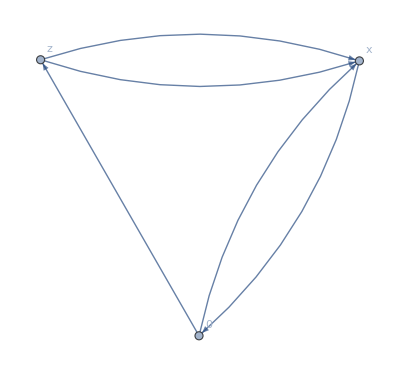
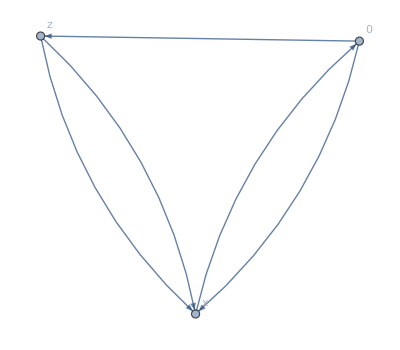
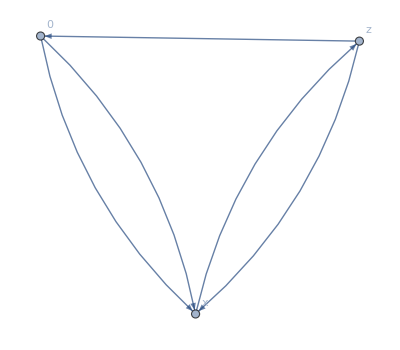
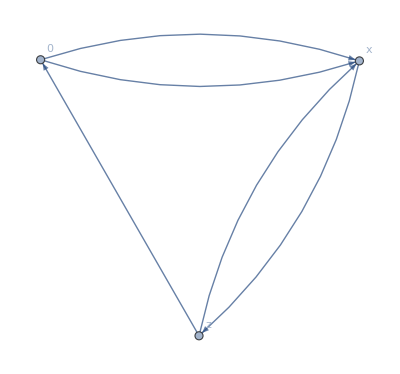
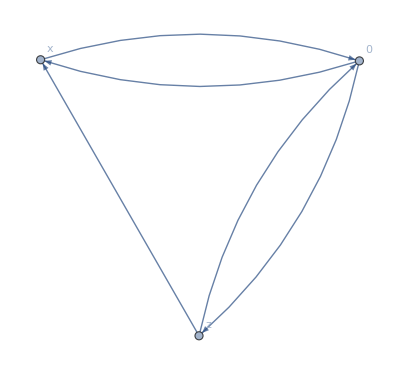
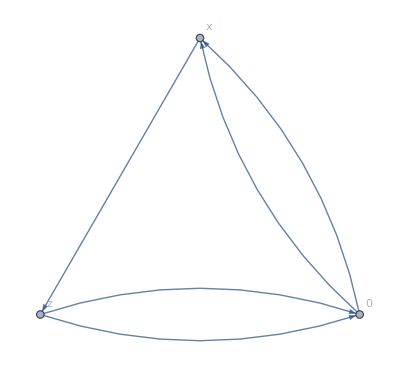
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pertQQA=pertConnectedQQA-Total@Cases[pertConnectedQQA,_. contract[op[__,x_],op[__,x_]],{1}];
toGraph/@List@@pertQQA
```

```mathematica
pertQQA[[1]]
```

1/(32 q.q)ⅇ^(ⅈ q x) contract[op[A,c,ω1,x],op[F,b,ω2,η2,0]] contract[op[A,d,η1,x],op[A,a15,ρ20,z]] contract[op[Q,α2,j,x],op[Q̄,α16,i18,z]] contract[op[Q,β17,j19,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] structure[a,c,d] g_s^4 dirac[γ[ρ]][i,j] dirac[γ[ρ20]][i18,j19] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a15][α16,β17] λ[b][β1,β2]

All of these diagrams go like g_s^4.

### 4d Gluon Condensate

```mathematica
prefactorQQA
Total@Cases[wickFermionQQA,_. normalOrder[{}],{1}]/.normalOrder[{}]->1
Total@Cases[wickBosonQQA,_. normalOrder[{_,_}],{1}]
```

-(ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^3 dirac[γ[ρ]][i,j] dirac[γ[ρ48]][i46,j47] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a43][α44,β45] λ[b][β1,β2])/(32 q.q)

-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α44,i46,z]] contract[op[Q,β45,j47,z],op[Q̄,α1,i,x]]+contract[op[Q,α2,j,x],op[Q̄,α44,i46,z]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] contract[op[Q,β45,j47,z],op[Q̄,α1,i,x]]+contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] contract[op[Q,β45,j47,z],op[Q̄,α44,i46,z]]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]] contract[op[Q,β45,j47,z],op[Q̄,α44,i46,z]]-contract[op[Q,α2,j,x],op[Q̄,α44,i46,z]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]] contract[op[Q,β45,j47,z],op[Q̄,β1,k,0]]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α44,i46,z]] contract[op[Q,β45,j47,z],op[Q̄,β1,k,0]]

contract[op[A,d,η1,x],op[F,b,ω2,η2,0]] normalOrder[{op[A,c,ω1,x],op[A,a43,ρ48,z]}] structure[a,c,d] g_s+contract[op[F,b,ω2,η2,0],op[A,a43,ρ48,z]] normalOrder[{op[A,c,ω1,x],op[A,d,η1,x]}] structure[a,c,d] g_s+contract[op[A,d,η1,x],op[A,a43,ρ48,z]] normalOrder[{op[A,c,ω1,x],op[G,b,ω2,η2,0]}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[F,b,ω2,η2,0]] normalOrder[{op[A,d,η1,x],op[A,a43,ρ48,z]}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,a43,ρ48,z]] normalOrder[{op[A,d,η1,x],op[G,b,ω2,η2,0]}] structure[a,c,d] g_s+contract[op[A,c,ω1,x],op[A,d,η1,x]] normalOrder[{op[G,b,ω2,η2,0],op[A,a43,ρ48,z]}] structure[a,c,d] g_s+contract[op[F,a,ω1,η1,x],op[A,f,η2,0]] normalOrder[{op[A,e,ω2,0],op[A,a43,ρ48,z]}] structure[b,e,f] g_s+contract[op[F,a,ω1,η1,x],op[A,a43,ρ48,z]] normalOrder[{op[A,e,ω2,0],op[A,f,η2,0]}] structure[b,e,f] g_s+contract[op[F,a,ω1,η1,x],op[A,e,ω2,0]] normalOrder[{op[A,f,η2,0],op[A,a43,ρ48,z]}] structure[b,e,f] g_s+contract[op[A,e,ω2,0],op[A,f,η2,0]] normalOrder[{op[G,a,ω1,η1,x],op[A,a43,ρ48,z]}] structure[b,e,f] g_s+contract[op[A,f,η2,0],op[A,a43,ρ48,z]] normalOrder[{op[G,a,ω1,η1,x],op[A,e,ω2,0]}] structure[b,e,f] g_s+contract[op[A,e,ω2,0],op[A,a43,ρ48,z]] normalOrder[{op[G,a,ω1,η1,x],op[A,f,η2,0]}] structure[b,e,f] g_s

All of these diagrams go like g_s^4.

### 6d Gluon Condensate

-(ⅇ^(ⅈ q x) leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] q[μ] q[ν] g_s^3 dirac[γ[ρ]][i,j] dirac[γ[ρ122]][i120,j121] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a117][α118,β119] λ[b][β1,β2])/(32 q.q)

contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]-contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α1,i,x]]-contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]]+contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,β1,k,0]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]]+contract[op[Q,α2,j,x],op[Q̄,α118,i120,z]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]]-contract[op[Q,α2,j,x],op[Q̄,α1,i,x]] contract[op[Q,β119,j121,z],op[Q̄,α118,i120,z]] contract[op[Q,β2,l,0],op[Q̄,β1,k,0]]

normalOrder[{op[G,a,ω1,η1,x],op[G,b,ω2,η2,0],op[A,a117,ρ122,z]}]

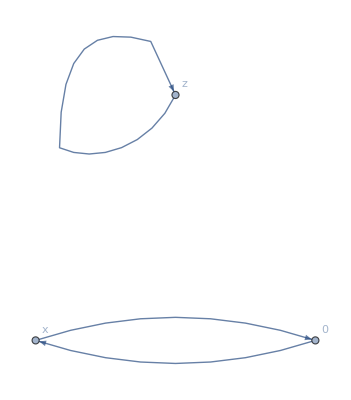
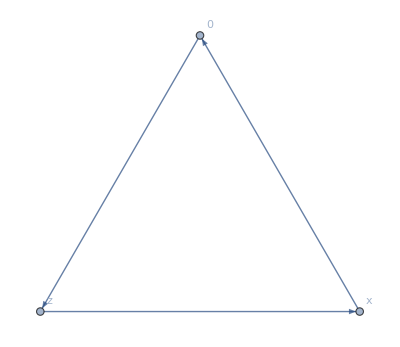
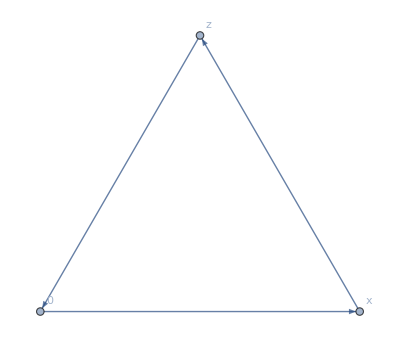
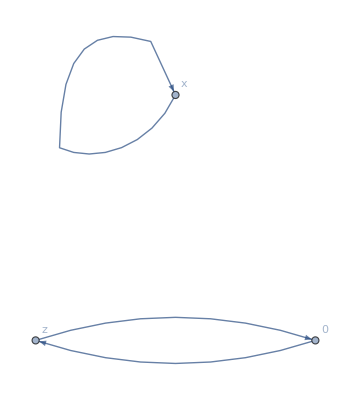
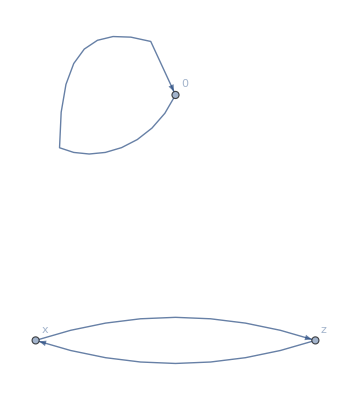
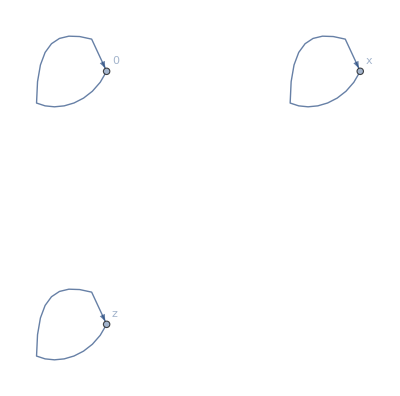

{-Graphics-,-Graphics-}

```mathematica
prefactorQQA
Total@Cases[wickFermionQQA,_. normalOrder[{}],{1}]/.normalOrder[{}]->1
Coefficient[Total@Cases[wickBosonQQA,_. normalOrder[{_,_,_}],{1}],Subscript[g, s],0]
gluonSixdRawQQA=Expand[%%% %% %];
toGraph/@List@@gluonSixdRawQQA
gluonSixdConnectedQQA=Pick[gluonSixdRawQQA,ConnectedGraphQ/@%];
toGraph/@List@@gluonSixdConnectedQQA
```

There are two diagrams; hence the explicit overall factor of 2.

```mathematica
2Total@Cases[gluonSixdConnectedQQA,_. contract[op[Q,__,x],op[OverBar@Q,__,0]]contract[op[Q,__,z],op[OverBar@Q,__,x]]contract[op[Q,__,0],op[OverBar@Q,__,z]],{1}]
%/.{
contract[op[Q,α_,i_,x],op[OverBar@Q,β_,j_,0]]:>Module[{p=p1},I Exp[-I p( x-0)]colourDelta[α,β]dirac[S[p,m]][i,j]],
contract[op[Q,α_,i_,z],op[OverBar@Q,β_,j_,x]]:>Module[{p=p2},I Exp[-I p( z-x)]colourDelta[α,β]dirac[S[p,m]][i,j]],
contract[op[Q,α_,i_,0],op[OverBar@Q,β_,j_,z]]:>Module[{p=p3},I Exp[-I p( 0-z)]colourDelta[α,β]dirac[S[p,m]][i,j]]
}//.diracIndexToMatrix;
Expand//@SToGamma//@%//.diracTraceLinear//Simplify;
Expand[%//.applyDiracTrace/.leviCivitaProductExpand//.normalToCondensates/.colourSimplify/.dStructure[_,_,_]->0/.colourSimplify]//.lorentzToDot;
gluonSixdIntegrandQQA=Simplify@%
```

1/(16 q.q)ⅇ^(ⅈ q x) contract[op[Q,α2,j,x],op[Q̄,β1,k,0]] contract[op[Q,β119,j121,z],op[Q̄,α1,i,x]] contract[op[Q,β2,l,0],op[Q̄,α118,i120,z]] leviCivita[η1,μ,ρ,ω1] leviCivita[η2,ν,σ,ω2] normalOrder[{op[G,a,ω1,η1,x],op[G,b,ω2,η2,0],op[A,a117,ρ122,z]}] q[μ] q[ν] g_s^3 dirac[γ[ρ]][i,j] dirac[γ[ρ122]][i120,j121] dirac[γ[σ]][k,l] λ[a][α1,α2] λ[a117][α118,β119] λ[b][β1,β2]

(2 (-3+dim) ⅇ^(-ⅈ (p1 x-q x-p3 z+p2 (-x+z))) (p1.q (-p2.z p3.q+p2.q p3.z)+((-2+dim) m^2-(-3+dim) p1.p3) p2.z q.q+2 m^2 p3.z q.q-dim m^2 p3.z q.q-3 p1.p2 p3.z q.q+dim p1.p2 p3.z q.q+2 m^2 p2.q q.z-dim m^2 p2.q q.z-3 p1.p3 p2.q q.z+dim p1.p3 p2.q q.z-2 m^2 p3.q q.z+dim m^2 p3.q q.z+3 p1.p2 p3.q q.z-dim p1.p2 p3.q q.z) vev[gggGGG])/((-2+dim) (-1+dim) dim (m^2-p1.p1) (m^2-p2.p2) (m^2-p3.p3) q.q)

```mathematica
tmp=gluonSixdIntegrandQQA;
Cases[tmp,Exp[a_]:>Collect[a,{x,z},Simplify],Infinity]
DeleteDuplicates@Cases[Expand[Numerator[tmp]],Dot[_,x|z]^(_.)|Dot[x|z,_]^(_.),Infinity]
```

{-ⅈ (p1-p2-q) x-ⅈ (p2-p3) z}

{p2.z,p3.z,q.z}

```mathematica
theExp=Times@@Cases[tmp,E^(_.),{1}];
List@@Expand[tmp/theExp];
Thread[dotToLorentz[%,z]];
%//.z[μ_]^(n_.)a_:>Nest[Expand[I momentumD[#,p3,μ]]&,a,n]//.lorentzToDot;
theExp Simplify[Total[%]];
%/.p3->p2/.p2->p1-q;
(MapAll[Distribute[#,Plus,Dot]&,Numerator[%]]//.(Dot[-p_,q_]|Dot[p_,-q_]):>-Dot@@Sort[{p,q}])/Denominator[%];
gluonSixdIntegrandFinalQQA=Simplify@Expand@%
```

-(2 ⅈ (-3+dim) (m^2-p1.p1+2 p1.q-q.q) (-2 (p1.q)^2+((-1+dim) m^2-(-3+dim) p1.p1) q.q+(-1+dim) p1.q q.q) vev[gggGGG])/((-1+dim) dim (m^2-p1.p1) (m^2-(p1-q).(p1-q))^3 q.q)

```mathematica
Clear[toTFI]
toTFI=dimReg[expr:Apply[Alternatives,(Times@@@Union[DeleteCases[Subsets[{k1.k1,k2.k2,k1.q,k2.q,k1.k2}^(_.)],{}],{{1}}])/((m^2-k1.k1)(k2.k2-Λ^2)(m^2-(k1-q).(k1-q))^3)],q,{k1,k2}]:>(-1)^4 π^dim TFI[dim,q.q,{Exponent[Numerator@expr,k1.k1],Exponent[Numerator@expr,k2.k2],Exponent[Numerator@expr,k1.q],Exponent[Numerator@expr,k2.q],Exponent[Numerator@expr,k1.k2]},{{1,m},{1,Λ},{3,m},0,0}];
```

```mathematica
Expand[1/(μ^(2ϵ)(2π)^dim)gluonSixdIntegrandFinalQQA tarcerTrickFactor]/.{p1->k1,r->k2};
dimReg[%,q,{k1,k2}]//.dimRegLinear//Simplify;
%/.toTFI;
TarcerRecurse@%;
gluonSixdExactQQA=%/.toExact/.dim->4+2ϵ//Simplify
```

-(2^(-5-2 ϵ) (m^2)^ϵ π^(-2-ϵ) (1+2 ϵ) μ^(-2 ϵ) (4 m^2 (1+ϵ) Gamma[-1-ϵ]+(1+2 ϵ) q.q Gamma[-ϵ] HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)]) vev[gggGGG])/((2+ϵ) (4 m^2-q.q))

```mathematica
tmp=gluonSixdExactQQA;
hyp=Cases[tmp,HypergeometricPFQ[_,_,_],Infinity]
hypCoeff=Coefficient[tmp,hyp[[1]]]
hypFree=tmp-hypCoeff hyp[[1]]//Simplify
(Normal@Series[hypCoeff,{ϵ,0,0}]hyp[[1]]/.hypExpand)+Normal@Series[hypFree,{ϵ,0,0}];
%/.toMSbar/.Log[m^2]->Log[m^2/μ^2]+2 Log[μ];
Collect[%,{ϵ,Hold@Hypergeometric2F1[__]},FullSimplify];
gluonSixdResultQQA=%
```

{HypergeometricPFQ[{1,-ϵ},{3/2},(q.q)/(4 m^2)]}

-(2^(-5-2 ϵ) (m^2)^ϵ π^(-2-ϵ) (1+2 ϵ)^2 μ^(-2 ϵ) q.q Gamma[-ϵ] vev[gggGGG])/((2+ϵ) (4 m^2-q.q))

-(2^(-3-2 ϵ) (m^2)^(1+ϵ) π^(-2-ϵ) (1+3 ϵ+2 ϵ^2) μ^(-2 ϵ) Gamma[-1-ϵ] vev[gggGGG])/((2+ϵ) (4 m^2-q.q))

-vev[gggGGG]/(64 π^2 ϵ)+((q.q)^2 Hold[Hypergeometric2F1[1,1,5/2,(q.q)/(4 m^2)]] vev[gggGGG])/(384 m^2 π^2 (-4 m^2+q.q))+((-12 m^2+7 q.q+2 (-4 m^2+q.q) Log[m^2/μ^2]) vev[gggGGG])/(128 π^2 (4 m^2-q.q))

## Results

```mathematica
pertResultNone
```

(m^4 (4 m^2-q.q) g_s^2)/(32 π^4 ϵ^2)+1/(691200 m^2 π^4)(14400 m^8 (-2+π^2)-35640 m^6 q.q-3600 m^6 π^2 q.q+360 m^4 (q.q)^2-747 m^2 (q.q)^3-360 m^2 (4 m^2-q.q) (40 m^4-21 m^2 q.q+(q.q)^2) HypergeometricPFQ[{1,1,1},{3/2,3},(q.q)/(4 m^2)]+20 q.q (-80 m^6+58 m^4 q.q+4 m^2 (q.q)^2+(q.q)^3) HypergeometricPFQ[{1,1,2},{5/2,4},(q.q)/(4 m^2)]+360 m^2 (480 m^6-100 m^4 q.q-(q.q)^3) Log[m^2/μ^2]+43200 m^6 (4 m^2-q.q) Log[m^2/μ^2]^2) g_s^2-(((q.q)^3-480 m^6 (1+2 Log[m^2/μ^2])+20 m^4 q.q (5+12 Log[m^2/μ^2])) g_s^2)/(3840 π^4 ϵ)

```mathematica
gluonFourdResultNone
```

-(q.q vev[αGG])/(24 π ϵ)+(q.q (2 m^2+q.q) Hold[Hypergeometric2F1[1,1,5/2,(q.q)/(4 m^2)]] vev[αGG])/(144 m^2 π)-(q.q (17+6 Log[m^2/μ^2]) vev[αGG])/(144 π)

```mathematica
gluonSixdResultNone
```

vev[gggGGG]/(64 π^2 ϵ)-((-16 m^6+8 m^4 q.q-6 m^2 (q.q)^2+(q.q)^3) Hold[Hypergeometric2F1[1,1,5/2,(q.q)/(4 m^2)]] vev[gggGGG])/(384 m^2 π^2 (-4 m^2+q.q)^2)+((256 m^4-200 m^2 q.q+31 (q.q)^2+6 (-4 m^2+q.q)^2 Log[m^2/μ^2]) vev[gggGGG])/(384 π^2 (-4 m^2+q.q)^2)

```mathematica
gluonSixdResultQQA
```

-vev[gggGGG]/(64 π^2 ϵ)+((q.q)^2 Hold[Hypergeometric2F1[1,1,5/2,(q.q)/(4 m^2)]] vev[gggGGG])/(384 m^2 π^2 (-4 m^2+q.q))+((-12 m^2+7 q.q+2 (-4 m^2+q.q) Log[m^2/μ^2]) vev[gggGGG])/(128 π^2 (4 m^2-q.q))

## Comparison With Berg et al

```mathematica
qqToz=q.q->4 m^2 z;
gsToαs=Power[Subscript[g, s],n_Integer?EvenQ]->(4π Subscript[α, s])^(n/2);
```

### Perturbation Theory

```mathematica
Map[Simplify,pertResultNone/.qqToz/.gsToαs];
Coefficient[%,ϵ,0];
pertHarnett=Total@Cases[Expand[%],_. HypergeometricPFQ[_,_,_],{1}]//Simplify
```

1/(270 π^3)m^6 (9 (-10+31 z-25 z^2+4 z^3) HypergeometricPFQ[{1,1,1},{3/2,3},z]+z (-10+29 z+8 z^2+8 z^3) HypergeometricPFQ[{1,1,2},{5/2,4},z]) α_s

```mathematica
pertBerg=(m^6 Subscript[α, s])/(5400 π^3)(180(z-1)(4 z^2-21z+10)HypergeometricPFQ[{1,1,1},{3/2,3},z]+20z(8 z^3+8 z^2+29z-10)HypergeometricPFQ[{1,1,2},{5/2,4},z])//Simplify
```

1/(270 π^3)m^6 (9 (-10+31 z-25 z^2+4 z^3) HypergeometricPFQ[{1,1,1},{3/2,3},z]+z (-10+29 z+8 z^2+8 z^3) HypergeometricPFQ[{1,1,2},{5/2,4},z]) α_s

```mathematica
pertHarnett/pertBerg
```

1

### 4d Gluon Condensate

```mathematica
Map[Simplify,gluonFourdResultNone/.qqToz/.gsToαs];
Coefficient[%,ϵ,0];
gluonFourdHarnett=Total@Cases[Expand[%],_. Hold[Hypergeometric2F1[1,1,5/2,_]],{1}]//Simplify
```

(m^2 z (1+2 z) Hold[Hypergeometric2F1[1,1,5/2,(4 m^2 z)/(4 m^2)]] vev[αGG])/(18 π)

```mathematica
gluonFourdBerg=vev[αGG]/(36π)m^2 z(4z+2)Hold[Hypergeometric2F1[1,1,5/2,z]]//Simplify
```

(m^2 z (1+2 z) Hold[Hypergeometric2F1[1,1,5/2,z]] vev[αGG])/(18 π)

```mathematica
gluonFourdHarnett/gluonFourdBerg//ReleaseHold
```

1

### 6d Gluon Condensate

```mathematica
gluonSixdHarnett=Collect[gluonSixdResultNone+gluonSixdResultQQA/.qqToz/.gsToαs,Hold[Hypergeometric2F1[1,1,5/2,_]],Simplify]
```

((7-20 z+10 z^2) vev[gggGGG])/(384 π^2 (-1+z)^2)+((1-2 z+2 z^2) Hold[Hypergeometric2F1[1,1,5/2,(4 m^2 z)/(4 m^2)]] vev[gggGGG])/(384 π^2 (-1+z)^2)

```mathematica
vev[gggGGG]/(384 π^2(z-1)^2)((4 z^2(z-1)-(4 z^3-6 z^2+2z-1))Hold[Hypergeometric2F1[1,1,5/2,z]]+31 z^2-50z+16+(z-1)(9-21z))
gluonSixdBerg=Collect[%,Hold[Hypergeometric2F1[1,1,5/2,z]],Simplify]
```

1/(384 π^2 (-1+z)^2)(16+(9-21 z) (-1+z)-50 z+31 z^2+(1-2 z+6 z^2+4 (-1+z) z^2-4 z^3) Hold[Hypergeometric2F1[1,1,5/2,z]]) vev[gggGGG]

((7-20 z+10 z^2) vev[gggGGG])/(384 π^2 (-1+z)^2)+((1-2 z+2 z^2) Hold[Hypergeometric2F1[1,1,5/2,z]] vev[gggGGG])/(384 π^2 (-1+z)^2)

```mathematica
gluonSixdHarnett/gluonSixdBerg//ReleaseHold
```

1